# NG22P06. Метод опорных векторов: ядра и штрафы

#### 1. Оптимизация вычисления ядра

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Dimensions[data=Rest[Import["NG22P06Problem.xlsx",{"Sheets","Гуд"}]]];
```

```mathematica
X=data⟦;;,{1,2}⟧;
Y = data⟦;;,3⟧//Round;
```

```mathematica
(*Ядра*)
```

```mathematica
Ker1=(1+#1.#2)^4&;
Ker2=Compile[{{x,_Real,1},{y,_Real,1}},(1+x.y)^4];
Ker3=Compile[{{x,_Real,1},{y,_Real,1}},(1+x.y)^4,Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
(*Функции для вычисления матриц*)
```

```mathematica
TableEnum[Ker_]:=Timing@Dimensions[Q=Table[Last[r]*Last[c]*Ker[Most[r],Most[c]],{r,data},{c,data}]];
TableInd[Ker_]:=Timing@Dimensions[Q=Table[Last[data⟦r⟧]*Last[data⟦c⟧]*Ker[Most[data⟦r⟧],Most[data⟦c⟧]],{r,Length@data},{c,Length@data}]];
QArray[Ker_]:=Timing@Dimensions[Q=Array[Last[data⟦#1⟧]*Last[data⟦#2⟧]*Ker[Most[data⟦#1⟧],Most[data⟦#2⟧]]&,{Length@data,Length@data}]];
QOuter[Ker_]:=Timing@Dimensions[Q=Outer[Last[#1]*Last[#2]*Ker[Most[#1],Most[#2]]&,data,data,1]];
```

```mathematica
ParTableEnum[Ker_]:=Timing@Dimensions[Q=ParallelTable[Last[r]*Last[c]*Ker[Most[r],Most[c]],{r,data},{c,data}]];
ParTableInd[Ker_]:=Timing@Dimensions[Q=ParallelTable[Last[data⟦r⟧]*Last[data⟦c⟧]*Ker[Most[data⟦r⟧],Most[data⟦c⟧]],{r,Length@data},{c,Length@data}]];
ParArray[Ker_]:=Timing@Dimensions[Q=ParallelArray[Last[data⟦#1⟧]*Last[data⟦#2⟧]*Ker[Most[data⟦#1⟧],Most[data⟦#2⟧]]&,{Length@data,Length@data}]];
ParOuter[Ker_]:=Timing@Dimensions@Parallelize[Q=Outer[Last[#1]*Last[#2]*Ker[Most[#1],Most[#2]]&,data,data,1]];
```

```mathematica
time=Table[First[Q[ker]],{ker,{Ker1,Ker2,Ker3}},{Q,{TableEnum,TableInd,QArray,QOuter,ParTableEnum,ParTableInd,ParArray,ParOuter}}];
```

```mathematica
time
```

{{72.1719,101.813,19.2656,74.2656,6.54688,4.90625,0.6875,6.875},{49.2031,81.75,19.4375,55.125,7.57813,4.65625,0.53125,7.42188},{50.25,82.3438,18.8438,57.1719,6.95313,4.65625,0.484375,6.45313}}

```mathematica
Grid[time,Frame->All]
```

72.1719 | 101.813 | 19.2656 | 74.2656 | 6.54688 | 4.90625 | 0.6875 | 6.875
49.2031 | 81.75 | 19.4375 | 55.125 | 7.57813 | 4.65625 | 0.53125 | 7.42188
50.25 | 82.3438 | 18.8438 | 57.1719 | 6.95313 | 4.65625 | 0.484375 | 6.45313

```mathematica
(*Из последовательных TableInd+Function самый медленный, Array+Function - быстрый; из параллельных TableEnum+Compile самый медленный, Array+Compile+ - самый быстрый*)
```

### 2. Радиально - базисная функция Гаусса в качестве ядра

```mathematica
iCold = Flatten[Position[Y,-1]];
iWarm = Flatten[Position[Y,1]];
```

```mathematica
Fig0=Graphics[
MapThread[{#2/.{-1->Blue,1->Red},Opacity[0.4],Point[#1]}&,{X,Y}],
Frame->True
]
```

```mathematica
KerS[σ_]:=Compile[
{{x,_Real,1},{y,_Real,1}},
Exp[-((x-y).(x-y))/(2 σ^2)],
Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"
];
```

```mathematica
(*σ=1 подходит*)
```

```mathematica
Plot3D[KerS[1][{x,y},Mean[X]],{x,-2,2},{y,-2,2},ColorFunction->"GreenPinkTones"]
```

```mathematica
Ker=KerS[1];
```

```mathematica
(*Вычисление матрицы Q*)
```

```mathematica
Dimensions[Q=ParallelArray[Last[data⟦#1⟧]*Last[data⟦#2⟧]*Ker[Most[data⟦#1⟧],Most[data⟦#2⟧]]&,{Length@data,Length@data}]];
```

```mathematica
(*SVM-классификатор*)
```

```mathematica
SVM[x_]:=Λs.(Y⟦iS⟧Ker[X⟦iS⟧,x])-w0
```

```mathematica
(*Отступы*)
```

```mathematica
M=Y⟦#⟧SVM[X⟦#⟧]&/@iO;
```

### 3. Инициализация множества опорных точек

```mathematica
ClearAll[InitSupport];
InitSupport[n_]:=Module[
{iSC,iSW,iS={},iC,iO},
Do[
iSC=RandomSample[iCold,1];
FixedPoint[(iSW=First[Nearest[X⟦iWarm⟧->iWarm,X⟦#⟧,1]];
First[Nearest[X⟦iCold⟧->iCold,X⟦iSW⟧,1]])&,iSC];
iS=Join[iS,iSW,iSC],
n
];
iS=DeleteDuplicates[iS];
iC={};
iO=Complement[Range[Length[X]],iS,iC];
Return[{iS,iC,iO}]
]
```

```mathematica
{iS,iC,iO}=InitSupport[3];
```

### 4. Решение задачи квадратичной оптимизации

```mathematica
(*Чтобы не считать лишние элементы матрицы Q, посчитаем отдельно Qss и Qcs*)
```

```mathematica
Dimensions[Qss=ParallelArray[Y⟦iS⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iS⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iS,Length@iS}]]
```

{6,6}

```mathematica
Dimensions[Qcs=ParallelArray[Y⟦iC⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iC⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iC,Length@iS}]]
```

{0}

```mathematica
ClearAll[SolveQP];
SolveQP[iS_,iC_,surCharge_]:=Module[
{
c=surCharge,
Λ=Table[Subscript[λ,i],{i,Length[iS]}],
Qss=ParallelArray[Y⟦iS⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iS⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iS,Length@iS}],
Qcs=ParallelArray[Y⟦iC⟦#1⟧⟧Y⟦iS⟦#2⟧⟧Ker[X⟦iC⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iC,Length@iS}],
Λs,w0
},
Λs=FindMinimum[{1/2 Qss.Λ.Λ + If[Length[Qcs]≠0,c Total[Qcs.Λ],0]-Total[Λ],Y⟦iS⟧.Λ+c Total[Y⟦iC⟧]==0},Λ]//Last//Values;
w0=Median[Map[Λs.(Y⟦iS⟧*Ker[X⟦iS⟧,#])&,X⟦iS⟧]-Y⟦iS⟧];
Return[{Λs,w0}]
]
```

```mathematica
{Λs,w0}=SolveQP[iS,iC,3]
```

{{1851.1,1532.49,-16.8313,-26.9988,-671.021,-342.242},-23.6179}

### 5. Опорные точки и точки-нарушители

```mathematica
(*Опорные точки и разделительная линия*)
```

```mathematica
{iS,iC,iO}=InitSupport[5];
```

```mathematica
Length/@{iS,iC,iO}
```

{9,0,4783}

```mathematica
{Λs,w0}=SolveQP[iS,iC,1000]
```

{{538.283,-69.9675,553.942,33.793,-71.3612,-264.882,-204.387,363.564,462.531},-12.8005}

Dot::dotsh: Tensors {} and {0.155609,-0.0797271,-0.121631,0.861902,-0.988803,0.11488,-0.0686871,0.699016,-0.804376} have incompatible shapes.

Dot::dotsh: Tensors {} and {0.174019,-0.0956018,-0.141144,0.856834,-0.999972,0.128437,-0.0817945,0.769217,-0.861772} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

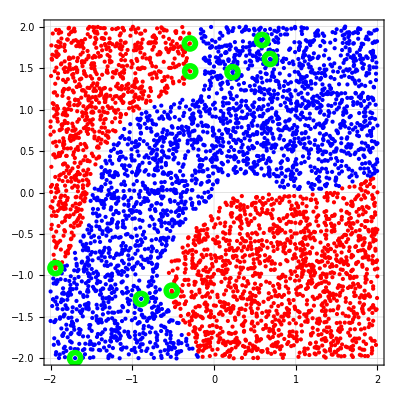

```mathematica
Show[
Fig0,
ContourPlot[
SVM[{x,y}],{x,-2,2},{y,-2,2},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.1],Blue},Opacity[0],Opacity[0],{Opacity[0.1],Red}}
],
{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧//Graphics
]
```

```mathematica
(*Ложная опорная точка с наименьшей лямбдой*)
```

```mathematica
iLC=First@TakeSmallest[Λs->"Index",1];
iS⟦iLC⟧
```

1701

```mathematica
(*Внутренняя точка с наименьшим отступом*)
```

```mathematica
M=Y⟦#⟧SVM[X⟦#⟧]&/@iO;
```

Dot::dotsh: Tensors {} and {0.669344,-0.45066,-0.5797,0.855979,-0.616736,0.57924,-0.424197,0.818736,-0.831751} have incompatible shapes.

Dot::dotsh: Tensors {} and {0.414493,-0.39659,-0.442169,0.496533,-0.515703,0.329365,-0.339248,0.895275,-0.803055} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
{Mn,iMn}=First[TakeSmallest[M->{"Element","Index"},1]]
```

{-6.05445,3989}

```mathematica
(*Добавляем в список нарушителей*)
```

```mathematica
iC=Join[iC,{iS⟦iLC⟧,iO⟦iMn⟧}]
```

{498,3995}

```mathematica
(*Наносим нарушителей на график*)
```

```mathematica
Show[
Fig0,
ContourPlot[
SVM[{x,y}],{x,-2,2},{y,-2,2},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.1],Blue},Opacity[0],Opacity[0],{Opacity[0.1],Red}}
],
{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧//Graphics,
{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧//Graphics
]
```

```mathematica
(*Убираем нарушителей из соответствующих списков*)
iS=Drop[iS,{iLC}];
iO=Drop[iO,{iMn}];
```

```mathematica
Length/@{iS,iC,iO}
```

{7,2,4743}

```mathematica
(*И убираем ложную опорную точку*)
```

```mathematica
AppendTo[iO,First[iC]];
iC=Drop[iC,{1}];
```

```mathematica
Length/@{iS,iC,iO}
```

{7,1,4744}

```mathematica
(*Заного просчитываем коэффицинты и строим график*)
```

```mathematica
{Λs,w0}=SolveQP[iS,iC,1000]
```

{{1008.37,1605.56,1389.69,-347.027,532.098,982.219,589.638},444.737}

```mathematica
Show[
Fig0,
ContourPlot[
SVM[{x,y}],{x,-2,2},{y,-2,2},
Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.1],Blue},Opacity[0],Opacity[0],{Opacity[0.1],Red}}
],
{Green,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iS⟧//Graphics,
{Gray,AbsoluteThickness[4],Circle[#,Offset[4]]}&/@X⟦iC⟧//Graphics
]
```